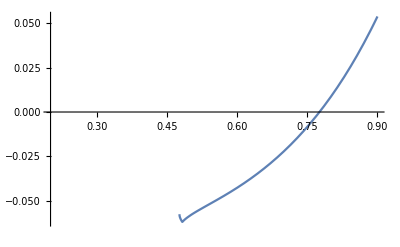

```mathematica
(* input rho1, th1, rho2 , rho1p *)
eps=1/4;
rho1=1.55;
th1=.;
rho2=2.0;
rho1p=1.95;
(* normal component of velovity ofr altra-relativistic fluid *)
vinn=N[√((3 rho1 + 1)/(3(3 + rho1)))];
v1n1=N[√((3+rho1)/(3(3 rho1+ 1)))];
v1n2=N[√((3 rho2/rho1 + 1)/(3(3 + rho2/rho1)))];
v2n=N[√((3  + rho2/rho1)/(3(3 rho2/rho1 +1)))];
vinnp=N[√((3 rho1p + 1)/(3(3 + rho1p)))];
v1pn1=N[√((3+rho1p)/(3(3 rho1p+ 1)))];
v1pn2=N[√((3 rho2/rho1p + 1)/(3(3 + rho2/rho1p)))];
v2np=N[√((3  + rho2/rho1p)/(3(3 rho2/rho1p +1)))];
(* compute the velocities and angles *)
vin=N[{vinn,0}/Cos[th1]];
n1={Cos[th1],Sin[th1]};
t1={-Sin[th1],Cos[th1]};
v1=v1n1 n1 +vin.t1 t1;
a2=v1.v1;
a1=-2  v1n2 v1[[1]];
a0=v1n2^2 -v1[[2]]^2;
th2=N[ArcCos[(-a1+√(a1^2-4 a0 a2))/(2 a2)]];
n2={Cos[th2],-Sin[th2]};
t2={Sin[th2],Cos[th2]};
v2=v2n n2 +v1.t2 t2;

th1p=N[ArcCos[vinn/vinnp Cos[th1]]];
n1p={Cos[th1p],-Sin[th1p]};
t1p={-Sin[th1p],-Cos[th1p]};
v1p=v1pn1 n1p +vin.t1p t1p;
a2p=v1p.v1p;
a1p=-2 v1pn2 v1p[[1]];
a0p=v1pn2^2-v1p[[2]]^2;
th2p=N[ArcCos[(-a1p+√(a1p^2-4 a0p a2p))/(2 a2p)]];
n2p={Cos[th2p],Sin[th2p]};
t2p={Sin[th2p],- Cos[th2p]};
v2p=v2np n2p +v1p.t2p t2p;
Plot[v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]],{th1,.2,.9}]
th1r=FindRoot[v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]],{th1,0.73}];
th1= th1 /. th1r;
vin=N[{vinn,0}/Cos[th1]];
n1={Cos[th1],Sin[th1]};
t1={-Sin[th1],Cos[th1]};
v1=v1n1 n1 +vin.t1 t1;
a2=v1.v1;
a1=-2  v1n2 v1[[1]];
a0=v1n2^2 -v1[[2]]^2;
th2=N[ArcCos[(-a1+√(a1^2-4 a0 a2))/(2 a2)]];
n2={Cos[th2],-Sin[th2]};
t2={Sin[th2],Cos[th2]};
v2=v2n n2 +v1.t2 t2;
th1p=N[ArcCos[vinn/vinnp Cos[th1]]];
n1p={Cos[th1p],-Sin[th1p]};
t1p={-Sin[th1p],-Cos[th1p]};
v1p=v1pn1 n1p +vin.t1p t1p;
a2p=v1p.v1p;
a1p=-2 v1pn2 v1p[[1]];
a0p=v1pn2^2-v1p[[2]]^2;
th2p=N[ArcCos[(-a1p+√(a1p^2-4 a0p a2p))/(2 a2p)]];
n2p={Cos[th2p],Sin[th2p]};
t2p={Sin[th2p],- Cos[th2p]};
v2p=v2np n2p +v1p.t2p t2p;
(* check parallelism *)
v2[[1]] v2p[[2]]-v2[[2]]v2p[[1]];
```

```mathematica
N[rho1]
```

1.55

```mathematica
N[rho1p]
```

1.95

```mathematica
th1
```

0.775867

```mathematica
th2
```

0.610068

```mathematica
th1p
```

0.828234

```mathematica
th2p
```

0.684208

```mathematica
vin
```

{0.901307,0.}

```mathematica
v1
```

{0.811896,-0.0877219}

```mathematica
v2
```

{0.669409,0.01188}

```mathematica
v1p
```

{0.821076,0.087416}

```mathematica
v2p
```

{0.729781,0.0129514}

```mathematica
v2-v2p
```

{-0.0603723,-0.00107142}